# Simulating a Four-Bit Adder Circuit.

### Boolean Components.

We construct a four-bit adder using only the fundamental Boolean logic gates introduced in the text. We discuss each of the Boolean gates below. First, the AND gate.

#### AND GATE

andgate[bit1_,bit2_]: bit1_,bit2_ are binary number input values

```mathematica
andgate[bit1_,bit2_]=Which[bit1==0 && bit2==0,0,bit1==0 && bit2==1,0,bit1==1&&bit2==0,0,bit1==1 && bit2==1,1,1==1,"you made incorrect entry"];
```

```mathematica
(* Truth table for AND gate *)
andtruthtable=Flatten[Table[{x,y,"|",andgate[x,y]},{x,0,1},{y,0,1}],1];
TableForm[andtruthtable]
```

0 | 0 | | | 0
0 | 1 | | | 0
1 | 0 | | | 0
1 | 1 | | | 1

#### XOR GATE

xorgate[bit1_,bit2_]: bit1_,bit2_ are binary number input values

```mathematica
xorgate[bit1_,bit2_]=Which[bit1==0 && bit2==0,0,bit1==0 && bit2==1,1,bit1==1&&bit2==0,1,bit1==1 && bit2==1,0,1==1,"you made incorrect entry"];
```

```mathematica
xortruthtable=Flatten[Table[{x,y,"|",xorgate[x,y]},{x,0,1},{y,0,1}],1];
TableForm[xortruthtable]
```

0 | 0 | | | 0
0 | 1 | | | 1
1 | 0 | | | 1
1 | 1 | | | 0

#### OR GATE

orgate[bit1_,bit2]: bit1_,bit2_ are binary number input values

-Graphics-

```mathematica
orgate[bit1_,bit2_]=Which[bit1==0 && bit2==0,0,bit1==0 && bit2==1,1,bit1==1&&bit2==0,1,bit1==1 && bit2==1,1,1==1,"you made incorrect entry"];
```

```mathematica
ortruthtable=Flatten[Table[{x,y,"|",orgate[x,y]},{x,0,1},{y,0,1}],1];
TableForm[ortruthtable]
```

0 | 0 | | | 0
0 | 1 | | | 1
1 | 0 | | | 1
1 | 1 | | | 1

#### Half-Adder

We combine the above gates to form complex logic gates. The half-adder circuit is shown below

halfadder[x0_,y0_]: x0,y0 represent X, Y input values; output consists of bit values for C and S respectively

```mathematica
halfadder[x0_,y0_]:={xorgate[x0,y0],andgate[x0,y0]}
```

```mathematica
(* Truth table for halfadder *)
halfaddertruthtable=Flatten[Table[{x,y,"|",halfadder[x,y]},{x,0,1},{y,0,1}],1];
TableForm[halfaddertruthtable]
```

0 | 0 | | | 0
0
0 | 1 | | | 1
0
1 | 0 | | | 1
0
1 | 1 | | | 0
1

#### Full Adder

Combining above components, we construct the full-adder

fulladder[x,y,c]: x, y, c are the two input, and carry bits respectively. Output is the sum and carry bit.

```mathematica
fulladder[x_,y_,c_]:=Module[{carry1},carry1=halfadder[x,y][[2]];ybit1=halfadder[x,y][[1]];ybit2=halfadder[ybit1,c][[2]];sumbit=halfadder[ybit1,c][[1]];carrybit=orgate[carry1,ybit2];{sumbit,carrybit}]
```

```mathematica
(* check for the integrity of the full adder *)
```

```mathematica
TableForm[Flatten[Table[{x,y,c,fulladder[x,y,c]},{x,0,1},{y,0,1},{c,0,1}],2]]
```

0 | 0 | 0 | 0
0
0 | 0 | 1 | 1
0
0 | 1 | 0 | 1
0
0 | 1 | 1 | 0
1
1 | 0 | 0 | 1
0
1 | 0 | 1 | 0
1
1 | 1 | 0 | 0
1
1 | 1 | 1 | 1
1

#### Ripple Circuit for a Four-Bit Adder

Finally, combing the full and half-adder components, we construct a four-bit adder.

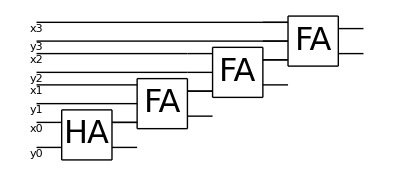

fourbitadder[xfourbitstring,yfourbitstring]: input values are two fourbit strings, xfourbitstring, yfourbitstring; ouput is the binary sum

```mathematica
fourbitadder[xfourbitstring_,yfourbitstring_]:=Module[{x0,x1,x2,x3,y0,y1,y2,y3},x0=xfourbitstring[[4]];x1=xfourbitstring[[3]];x2=xfourbitstring[[2]];x3=xfourbitstring[[1]];y0=yfourbitstring[[4]];y1=yfourbitstring[[3]];y2=yfourbitstring[[2]];y3=yfourbitstring[[1]];carry0=halfadder[x0,y0][[2]];sum0=halfadder[x0,y0][[1]];carry1=fulladder[x1,y1,carry0][[2]];sum1=fulladder[x1,y1,carry0][[1]];carry2=fulladder[x2,y2,carry1][[2]];sum2=fulladder[x2,y2,carry1][[1]];
carry3=fulladder[x3,y3,carry2][[2]];sum3=fulladder[x3,y3,carry2][[1]];{carry3,sum3,sum2,sum1,sum0}]
```

### Examples:

```mathematica
registerx={1,1,0,0};
registery={0,1,1,1};
```

```mathematica
fourbitadder[registerx,registery]
```

{1,0,0,1,1}

```mathematica
registerx={1,0,0,1};
registery={0,1,1,1};
```

```mathematica
fourbitadder[registerx,registery]
```

{1,0,0,0,0}